```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
MemoryInUse[](*useful function when using many scatterers!*)
```

31761992

```mathematica
Names["MultipleScattering2D`*"]
```

{AcousticImpulse,AcousticScattering,CombineWaves,ConvolutionTest,ExportListWave,FrequencyFromCoefficients,ImportListWave,ListenersOutsideScatterers,listWaveFromCoefficients,PlotWaves,ReplaceMiddleZero,ScatteringCoefficients,SeveralScattererCoefficients,SingleScattererCoefficients,WaveFθFromCoefficients}

### Two body Scattering!

|Wi[k]|_θ: 3.09522

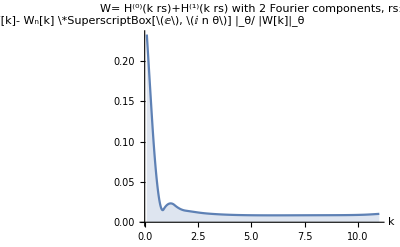

```mathematica
(*radius of the scatterers*)
radius=0.1; 
(*max number of hankel functions per scatterer*)
N0=2;
(*max angular frequency*)
Maxω=1.1/radius ;

options={
"PrintChecks"-> False,
"Maxk"-> Maxω, 
"SourcePosition"-> {0,0},
"BoundaryCondition"-> "Dirchlett"(*"BoundaryCondition"-> "Neumann"*)};

(*Position of the scatterers*)
Xs={{-.3,.4},{0.,.4}};

(*Return a function that give frequency ω returns a list of the scattering coefficients*)
scatteringCoefficients=SeveralScattererCoefficients[N0,Xs,radius,options];


To run a bunch of convergence checks uncomment below (takes a while!);
(*options=options~Join~{"PrintChecks"-> True};
coeffFk=SeveralScattererCoefficients[N0,Xs,radius,options];*)
```

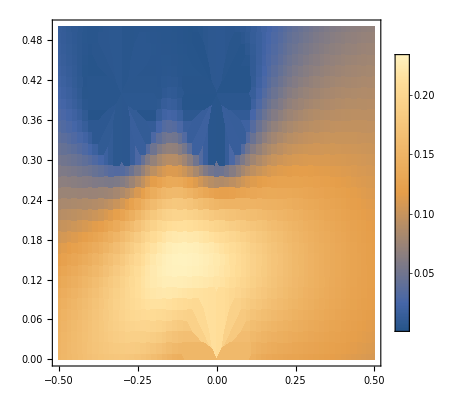

```mathematica
Calculate the response for a given frequency and position;

(*specify frequecny*)
	k = 10.1;
(*Choose listener positions*)         
	listeners={{0,0},{0,1}};
(*Calcualted scatterd wave*)         
	responses =FrequencyFromCoefficients[k,Xs,scatteringCoefficients,listeners];

Or for a whole field map use;
(*choose mesh*)
	rngX=Range[-5 radius,5 radius,radius/6];
	rngY=Range[0.,5 radius,radius/6];
(*exclude listeners inside any scatterer Xs and too close to the source {0,0}*)
	listeners = ListenersOutsideScatterers[radius,Xs~Join~{{0,0}},rngX,rngY];
	scatteredResponses =FrequencyFromCoefficients[k,Xs,scatteringCoefficients,listeners];

(*Default source is a green's function with scattering coefficients*)
	sourceCoefficient = {{ⅈ/4}}&;
	sourceResponses =FrequencyFromCoefficients[k,{{0,0}},sourceCoefficient,listeners];
(*plot result*)

responses= sourceResponses+scatteredResponses;
data = Flatten@{listeners[[#]],Abs@responses[[#]]}&/@Range[Length@responses];
ListDensityPlot[data,InterpolationOrder->0,PlotLegends->Automatic ]
```

```mathematica
Calculate fields  in time;
(*choose angular frequency range*)
	Nω= 45;(*number mesh points in frequency*)
	(*The parts below  with δ are to avoid using 
ω==0 and instead use a offset discrete Fourier transform. See notes DiscreteFourier.pdf.*) 
         cδ=0.3; (*leave as is*) 
	δω=Maxω/Nω(1 + cδ/Nω)^-1 ; (*δω ≃ Maxω/Nω;*)
	δ = cδ δω;
	T=2π Nω /(Maxω-δ);
	δt=π/(Maxω-δ)2/(2+1/Nω);

	Print["Resulting in time t ∈ Range[0, ",T,",",δt,"]" ];
	rngω=Range[0,Maxω,δω];
	(*frequencies needed to do the offset discrete Fourier*)
         rngωFourier=  rngω~Join~Reverse@Drop[-rngω,1] +δ;
```

Resulting in time t ∈ Range[0, 25.8753,0.284344]

```mathematica
(*Calculate the scattering coefficients for the given frequency range*)
	listScatteringCoefficients= Transpose/@Transpose[scatteringCoefficients/@rngωFourier];
	sourceCoefficient = {ⅈ/4}&;
	listSourceCoefficient=  Transpose[sourceCoefficient/@rngωFourier ];
	(*add the source as a scatterer*)
	Xs = Xs~Join~{"SourcePosition"/.options};

(*Choose the mesh in cylindrical coordinates for the radius and angle*)
	rngr=Range[radius,10Max@Abs@Xs,radius];
	rngθ= Range[0,2π+.1,.1];

(*Impulse to convolute in time with the source *)	
	timeImpulse = If[0≤ N[#//Chop,4]≤ T/(2Nω+1) ,1,0]&;

options={
"PrintChecks"-> False,
"ImpulsePeriod"->T/(2 Nω +1),
"MaxTimeSamples"-> 35,
"MaxTime"-> 6,
"Impulse"-> timeImpulse
};

(*Calculate fields in time*)
	listWaves= Re@listWaveFromCoefficients[#,rngωFourier,rngθ,rngr,options]&/@listScatteringCoefficients;
         (*Add wave from the source*)	
         listWaves~AppendTo~ Re[listWaveFromCoefficients[listSourceCoefficient,rngωFourier,rngθ,rngr,options] ];
```

```mathematica
(*Save the result as a gif!*)
	options={"PlotAmplitude"-> .6,"MeshSize"-> radius/2};
	timeplots= CombineWaves[Xs,listWaves,options];
	Export[NotebookDirectory[]<>"TwoBodyScattering.gif",timeplots];

(*Alternatively, plot without source:*)
	timeplots2= CombineWaves[Drop[Xs,-1],Drop[listWaves,-1],options];
	Export[NotebookDirectory[]<>"TwoBodyNoSource.gif",timeplots2];
```

Mesh Size:0.05

InterpolatingFunction::dmval: Input value {-2.8256,2.8244} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Amp: 0.0811306

Mesh Size:0.05

InterpolatingFunction::dmval: Input value {-2.8256,3.2244} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Amp: 0.0811306

```mathematica
(*To export listWaves:*)
	Header={Xs,radius,N0,{Maxω,Nω,δ}};
	ExportListWave[Header,listWaves];
```

```mathematica
(*To import*)
	{Header,listWaves}=ImportListWave[Length@Xs,N0,Nω];
	{Xs,radius,N0,{Maxω,Nω,δ}}=Header;
```

Mesh Size:0.0333333

Amp: 0.136774